```mathematica
Clear["Global`*"]
```

#### New Calibration trace at YOKO=0mA, 6.3~6.6GHz, 5dBm 10us integration 50Kavg,100KHz step

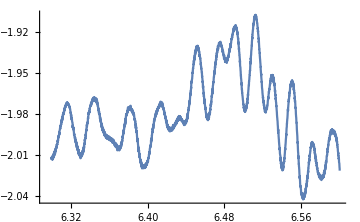
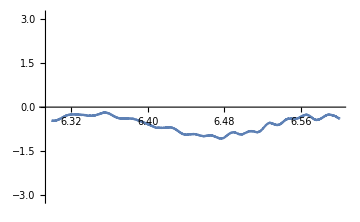

```mathematica
file="D:\\Travail Nath\\JQI\\branching_ratio_paper\\Data analysis package with 02 pumping\\one_tone_6.3GHz_to_6.6GHz_5dBm_0mA_10us integration_50Kavg_100KHz step_062318.dat";
data=Import[file];
header=Take[data,1];
ref=Drop[data,1];
edelay = 322.0;
ampref=ref[[;;,3]];
phaseref=ref[[;;,2]];
Row@{ListLinePlot[{#[[1]],Log10@#[[3]]}&/@ref,PlotRange->All,ImageSize->Medium],
ListLinePlot[{#[[1]],Arg[Exp[I(#[[2]]-edelay*#[[1]])]]}&/@ref,PlotRange->{-Pi,Pi},ImageSize->Medium]}
```

#### T1 of 01 with 0-2 pumping(-10dBm, 50us), 1us integration, with 500 ns delay, avg up to 150K up to 150us(two time segments)

{/delay_table,/demod_Magnitude0,/demod_Phase0}

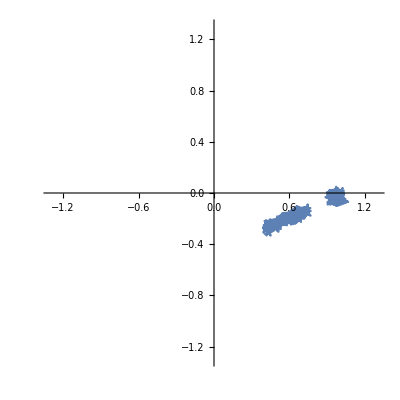

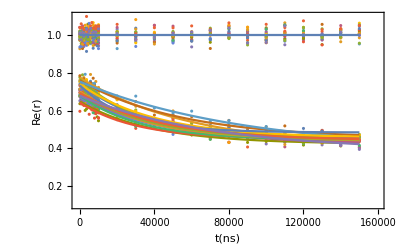

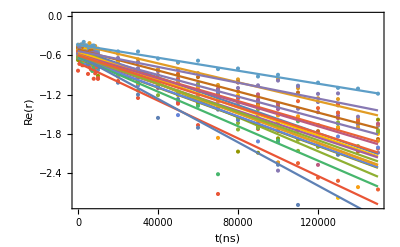

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

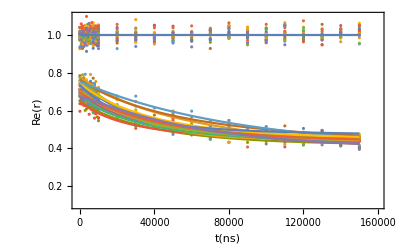

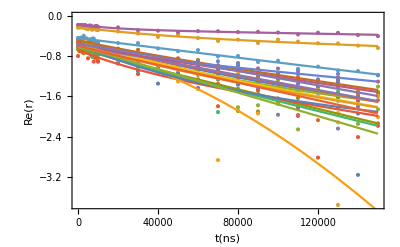

```mathematica
file="D:\\TRAVAI~1\\JQI\\BRANCH~1\\DATAAN~1\\062618~1.H5";(*"D:\\Travail Nath\\JQI\\branching_ratio_paper\\Data analysis package with 02 pumping\\062618_t1_readout_6.5319GHz__-15dBm_qubit3.8355GHz_-10dBm_-0.6_mA_delay to10000ns_15points_ to150000ns_15points_ duty210us_1us integration_500ns delay_avg100k_50us  pulse_loop20.h5";*)
header=Import[file]
edelay1 = 322;
edelay2 = 322;
Freadout1=6.4819;
Freadout2 = 6.5819;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=0.6π/2;
phaseoffset2 = -1.05π / 2;
powerRef=5;
numberloop =20;
numberRabidata =30;
initguessS={{A,0.5},{B,0.2},{TR,20000}};
BoundS={1>A>0,1>B>0,TR>0};
initguessD={{A1,0.5},{A2,0.9},{B,0.2},{TR1,40000},{TR2,6000}};
BoundD={1>A1>0,1>B>0,TR1>0,TR2>0};
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",1}];
(*ListLinePlot[delays]*)
amp=Flatten@Import[file,{"Datasets",2}];
(*ListLinePlot[amp]*)
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",3}];
(*ListLinePlot[phase]*)
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]];
(*p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{-0.5,1.3}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
shift2=1-avgRef2;
(*p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{-0.5,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]*)
scale2=1/avgRef2;
scalefit2=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{A*Exp[-t/TR]+B,BoundS},initguessS,t],{loopi,1,numberloop}];
Rabirefl2table=ArrayReshape[Rabirefl2,{10,30}];
listplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,160000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
listplottable2=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Re[Refrefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2},{loopi,1,numberloop}],PlotRange->{{-1000,160000},{0.1,1.1}}, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
fit2table=A*Exp[-t/TR]+B/.scalefit2;
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
loglistplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Log10[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2-B/.scalefit2[[loopi]]]},{loopi,1,numberloop}],PlotRange->All, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
logfit2table=Log10[A*Exp[-t/TR]/.scalefit2];
log10p3=Show[loglistplottable,Plot[logfit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
Clear[A1,A2,B,TR1,TR2];
model=A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]+B;
scalefit2=Table[FindFit[Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}],{model,BoundD},initguessD,t],{loopi,1,numberloop}];
fit2table=A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]+B/.scalefit2;
(*scalefit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]*scale2}],A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]+B,{{A1,0.4},{A2,0.1},B,{TR1,25000},{TR2,2000}},t]*)
p03drive10usscale100us=Show[listplottable,listplottable2,Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All],Plot[fit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
loglistplottable=ListPlot[Table[Transpose@{delays[[numberRabidata (loopi-1)+1;;numberRabidata loopi]],Log10[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2-B/.scalefit2[[loopi]]]},{loopi,1,numberloop}],PlotRange->All, LabelStyle->Large, FrameLabel->{t[ns],Re[r]}];
logfit2table=Log10[A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]/.scalefit2];
log10p3=Show[loglistplottable,Plot[logfit2table,{t,0,delays[[-1]]},PlotRange->All], Frame->True]
```

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | 0.369643 | 0.0209638 | {0.326629,0.412657}
B | 0.404236 | 0.0230904 | {0.356859,0.451614}
TR | 59966.7 | 9405.45 | {40668.3,79265.1}

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A1 | 0.606445 | 4.74406 | {-9.16414,10.377}
A2 | 0.408534 | 2.00968 | {-3.73047,4.54754}
B | 0.172413 | 4.74921 | {-9.60876,9.95359}
TR1 | 313222. | 5.89983×10^6 | {-1.18377×10^7,1.24641×10^7}
TR2 | 44979.7 | 51004.3 | {-60065.7,150025.}

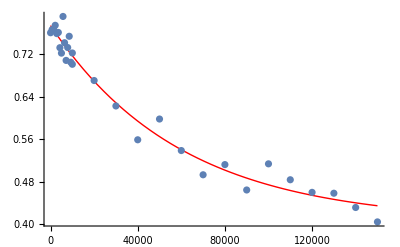

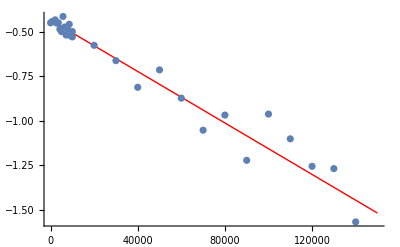

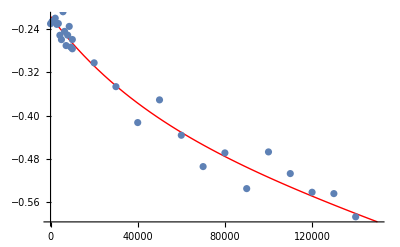

-Graphics-

-Graphics-

```mathematica
loopi=2;
model=A*Exp[-t/TR]+B;
model2=A1*Exp[-t/TR1+A2*(Exp[-t/TR2]-1)]+B;
data=Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
nmf2=NonlinearModelFit[data,{model2,BoundD},initguessD,t];
sparam=nmf["BestFitParameters"];
dparam=nmf2["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
nmf2["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays[[1;;numberRabidata]],Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2/.sparam}];
Show[Plot[nmf[t]/.sparam,{t,0,delays[[-1]]},PlotStyle->{Red,Thick},PlotRange->All],ListPlot[dataS,PlotRange->All]]
logdataS=Transpose[{delays[[1;;numberRabidata]],Log10[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2-B/.sparam]}];
Show[Plot[Log10[nmf[t]-B/.sparam],{t,0,delays[[-1]]},PlotStyle->{Red,Thick},PlotRange->All],ListPlot[logdataS,PlotRange->All]]

logdataD=Transpose[{delays[[1;;numberRabidata]],Log10[Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2-B/.dparam]}];
Show[Plot[Log10[nmf2[t]-B/.dparam],{t,0,delays[[-1]]},PlotStyle->{Red,Thick},PlotRange->Automatic],ListPlot[logdataD,PlotRange->Full]]
P0ini=0.64;
r0=0.658;
dataS=Transpose[{delays[[1;;numberRabidata]]/1000,(1-(Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2))*(P0ini/r0)/.sparam}];
Show[ListPlot[dataS,PlotRange->All,PlotMarkers->{"●"},LabelStyle->Large,FrameLabel->{t[us],P0}],Plot[(1-(nmf[t*1000]/.sparam))*(P0ini/r0),{t,0,delays[[-1]]/1000},PlotStyle->{Red,Thick},PlotRange->All],FrameTicks->{{Table[0.05i,{i,-5,5}],None},{Table[20i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
dataS=Transpose[{delays[[1;;numberRabidata]]/1000,((Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2)-B)*(P0ini/r0)/.sparam}];
Show[ListLogPlot[dataS,PlotRange->Automatic,PlotMarkers->{"●"},LabelStyle->Large,FrameLabel->{t[us],Δ(1-P0)}],LogPlot[((nmf[t*1000]-B/.sparam))*(P0ini/r0),{t,0,delays[[-1]]/1000},PlotStyle->{Red,Thick},PlotRange->Automatic],(*FrameTicks->{{Table[0.05i,{i,-5,5}],None},{Table[20i,{i,0,7}],None}},*) Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

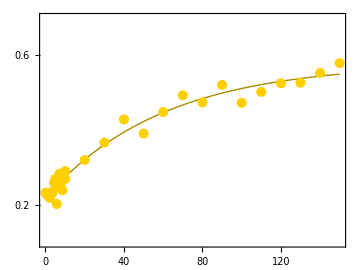

```mathematica
dataS=Transpose[{delays[[1;;numberRabidata]]/1000,(1-(Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2))*(P0ini/r0)/.sparam}];
Show[Plot[(1-(nmf[t*1000]/.sparam))*(P0ini/r0),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[1,0.81,0],Thick],PlotRange->{0.1,.7}],ListPlot[dataS,PlotStyle->Directive[PointSize[0.02],RGBColor[1,0.81,0]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[20i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

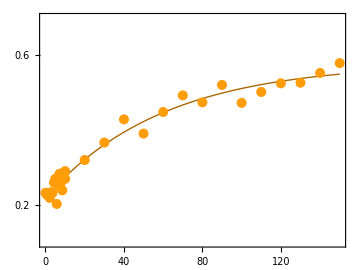

```mathematica
dataS=Transpose[{delays[[1;;numberRabidata]]/1000,(1-(Re[Rabirefl2[[numberRabidata (loopi-1)+1;;numberRabidata loopi]]]*scale2))*(P0ini/r0)/.sparam}];
Show[Plot[(1-(nmf[t*1000]/.sparam))*(P0ini/r0),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{0.1,.7}],ListPlot[dataS,PlotStyle->Directive[PointSize[0.02],RGBColor["#FF9D08"]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[20i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```